CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\search\\" already exists.

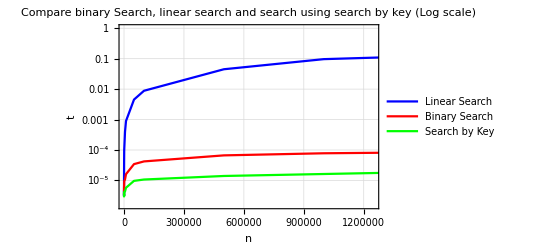

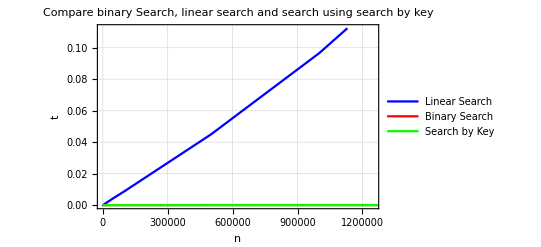

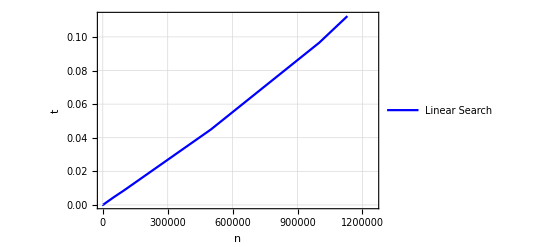

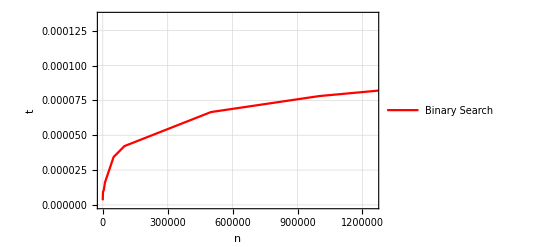

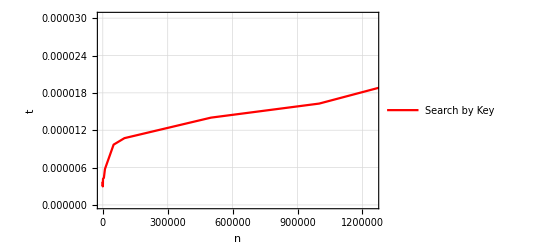

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = "../shown results";
SetDirectory[workingDirectory];
file= OpenRead["../logs/log_search.txt"];
workingDirectory = CreateDirectory["search"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

mapSearchResults = filelist[[3;;;;4]];
binarySearchResults = filelist[[2;;;;4]];
linearSearchResults = filelist[[1;;;;4]];
linearSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,linearSearchResults];
binarySearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,binarySearchResults];
mapSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,mapSearchResults];
linearSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,linearSearchResults];
binarySearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,binarySearchResults];
mapSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,mapSearchResults];
Plot1 = Show[ListLogPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key (Log scale)", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListLogPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}],
ListLogPlot[mapSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Search by Key"}]]
Plot2 = Show[ListPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}],
ListPlot[mapSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Search by Key"}]]
Plot3 = ListPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot4 = ListPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot5 = ListPlot[mapSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Search by Key"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Linear.gif",Plot3,ImageSize->2048];
Export["Binary.gif",Plot4,ImageSize->2048];
Export["Map.gif",Plot5,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Number"},binarySearchResults[[All,1]]],Join[{"Linear Search (sec.)"},linearSearchResults[[All,2]]],Join[{"Binary Search (sec.)"},binarySearchResults[[All,2]]],Join[{"Search by Key (sec.)"},mapSearchResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Number | Linear Search (sec.) | Binary Search (sec.) | Search by Key (sec.)
5 | 4.64797×10^-6 | 3.3027×10^-6 | 3.15241×10^-6
10 | 3.11575×10^-6 | 3.57029×10^-6 | 2.97646×10^-6
50 | 6.02623×10^-6 | 4.51968×10^-6 | 3.6326×10^-6
100 | 0.0000110004 | 5.61935×10^-6 | 3.69858×10^-6
500 | 0.0000410363 | 6.61639×10^-6 | 3.11209×10^-6
1000 | 0.0000992093 | 9.38025×10^-6 | 4.2081×10^-6
5000 | 0.00039856 | 0.0000108245 | 4.34373×10^-6
10000 | 0.000899071 | 0.0000160883 | 5.76964×10^-6
50000 | 0.00453388 | 0.0000343906 | 9.6845×10^-6
100000 | 0.00882628 | 0.000042202 | 0.0000107255
500000 | 0.044953 | 0.0000666295 | 0.0000140209
1000000 | 0.0965481 | 0.0000780881 | 0.0000162789
5000000 | 0.582974 | 0.000135436 | 0.0000531328

```mathematica
Export["TableSerch.gif",grid,ImageSize->{2048,720}];
Export["TableSeach.xls",grid,ImageSize->{2048,720}];
```